# Bird’s Eye View of Convention Sign-up

<|A→0.0379425,B→0.0850223,«23»,Z→0.00566274|>

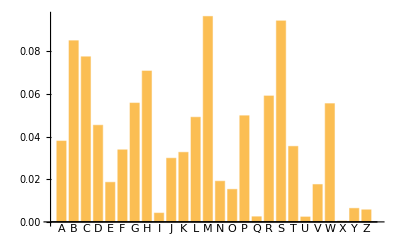

```mathematica
percents = CloudGet["https://www.wolframcloud.com/objects/e338adb3-f090-4867-8456-f3f66c422f38"];
Print[Short[percents]];
BarChart[percents, ChartLabels -> Keys@percents]
```

These are the pairs of letters (first and last) in each table’s range. Let’s make labels for them and get the whole alphabet for looking up the indices.

```mathematica
tables = { { "A", "F" }, { "G", "M" }, { "N", "S" }, { "T", "Z"} };
alphabet = Keys@percents
labels = StringJoin[First@#, "-", Last@#]& /@ tables
```

{A,B,C,D,E,F,G,H,I,J,K,L,M,N,O,P,Q,R,S,T,U,V,W,X,Y,Z}

{A-F,G-M,N-S,T-Z}

We need to get the index of each letter at the start or end of a range. It’s easiest to take a second-level Map of the Position in the full alphabet, Flatten the results and repartition them:

```mathematica
indices = Partition[Flatten@Map[Position[alphabet, #]&, tables, {2}], 2]
```

{{1,6},{7,13},{14,19},{20,26}}

Great. Now we just need to sum the percents bounded by each of the four groups and make sure it sums to one. Remember, we can use Take and Total on Associations with Numbers as values, same as an array

```mathematica
queues = Map[
	Total[Take[percents, {First@#, Last@#}]]&,
	indices
]
Total@queues
queuesWithLabels = AssociationThread[labels, queues]
```

{0.298155,0.338703,0.239977,0.123164}

1.

<|A-F→0.298155,G-M→0.338703,N-S→0.239977,T-Z→0.123164|>

We want to draw our lines all in the same Graphics object, rather than using Show to combine the individual lines, since otherwise we’d have to carefully calibrate the scales to make every person the sample size

t_ will stand for “tier” and increment up, while n_ is the total number of people in the line. This will return a lines of Disk[] and a Text[] object for the label

```mathematica
DrawLine[t_, n_] := (
	label = Keys[queuesWithLabels][[t]];
	value = Values[queuesWithLabels][[t]];
	headCount = Round[n * value];
	heads = Table[Disk[{4 * x + 8, (5 - t) * 12 }, 1.6], {x, 1, headCount }];
	Prepend[heads, Text[Style[label, FontSize->13, Red, Bold], {0, (5 - t) * 12 }]]
)
```

Here’s what 250 people looks like

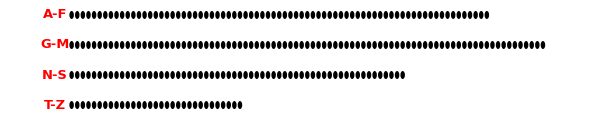

```mathematica
Graphics[	
	DrawLine[#, 250]& /@ Range[4],
	ImageSize->600
]
```